# HW #2 Albert Liu

## 1) Linear Transformation of an image

a) Linear Transformation defines that T(a+b) = T(a) + T(b) and T(c*a) = c*T(a). This applies to the image matrix.
Image Transformation is to change the image’s position (translation), size (scaling), orientation(rotation) and shapes(shear).

b) Alter the size of an object by a scaling factor (sx, sy).

```mathematica
MatrixForm[{{x}, {y}}] == MatrixForm[{{sx, 0}, {0, sy}}] MatrixForm[{{x}, {y}}]
```

(x
y)==(x
y) (sx | 0
0 | sy)

The formula shows that T(s*r) = s*T(r), and T(v1 + v2) = T(v1) + T(v2). sx = sy = 3 in this case. It is linear.

c) say we have two vector: a and b. T is the linear transformation that give us the median. Since T(a+b) != T(a) + T(b), it is NOT linear. (In fact, it does satisfy T(c*a) = c*T(a), aka close under multiplication. Since it does NOT close under addition, it is NOT linear)

## 2)

```mathematica
R= Import[NotebookDirectory[]<>"rubberband.jpg"]
```

-Graphics-

#### a) size of R

```mathematica
ImageDimensions[R]
Dimensions[R]
```

{640,480}

{}

The dimensions of R returns nothing since the parameter cannot be an image, while ImageDimensions return the actual size of R in {width, height}
In fact, R basically is just a file pointer. Its an object contains the memory address where we store the image. The ImageData pulls the image data out from the address indicate by the file pointer.

#### b) ImageResize

```mathematica
im2 = ImageResize[R,ImageDimensions[R][[1]]*2/3]
```

-Graphics-

#### C) Resize the new image to x1.5

```mathematica
im3 = ImageResize[im2,ImageDimensions[im2][[1]]*3/2]
```

-Graphics-

the new image has the same size compare to the original image R, but it seems the quality of new image is worse than the original image.

#### d) Convert to black and white

```mathematica
im4 = ColorConvert[im3, "Grayscale"]
```

-Graphics-

#### e) Rotate 27 degree left

```mathematica
im5 = ImageRotate[im3, 27°]
ImageDimensions[im5]
```

-Graphics-

{790,719}

### f) Rotate them back

```mathematica
im6 = ImageRotate[im5, -27°]
ImageDimensions[im6]
```

-Graphics-

{1031,1000}

The figure still looks identical to the original one but the dimension become much larger.

## 3) Histogram

### a) ImageHistogram

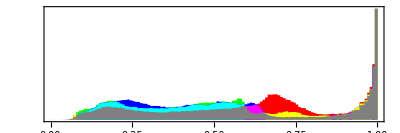

```mathematica
ImageHistogram[R]
```

### b) Histogram

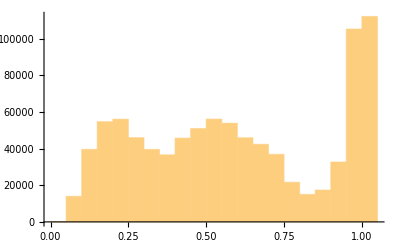

```mathematica
Histogram[Flatten[ImageData[R]]]
```

### c) Histogram3D

```mathematica
Dimensions@Map[{First[#],Mean[Rest[#]]}&,Flatten[ImageData[R],1]]
Histogram3D[Map[{First[#],Mean[Rest[#]]}&,Flatten[ImageData[R],1]]]
```

{307200,2}

-Graphics3D-

The ImageHistogram plots the distribution of pixel levels for each channel (All three channels in one figure).  Histogram plots the square box with x as the value and y as its frequency. Histogram3D shows a histogram as R is one axis and G,B as the other axis. The figure shows the frequency of distribution given the R value on one axis and G,B on the other axis.